```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/SIGW_QCD/math/YT

```mathematica
bgdata=Import["data/bg.csv"];
```

```mathematica
wList=Map[{#[[1]],#[[4]]}&,bgdata];
cs2List=Map[{#[[1]],#[[5]]}&,bgdata];
```

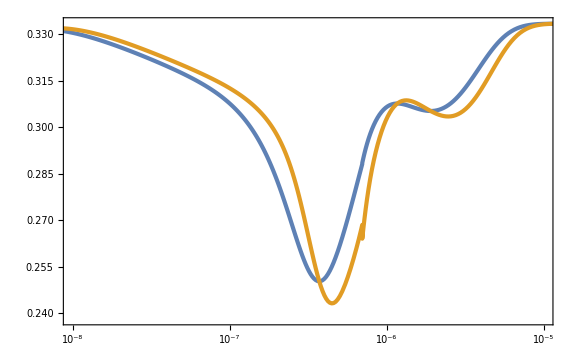

```mathematica
ListLogLinearPlot[{wList,cs2List},PlotRange->{{10^-8,10^-5},Full}]
```

## Check

```mathematica
DSolve[{Phi''[x]+3/x(1+1/3)Phi'[x]+1/3 Phi[x]==0,Phi[0]==1},Phi[x],x]
```

{{Phi[x]→-(9 (x Cos[x/(√3)]-√3 Sin[x/(√3)]))/x^3}}

```mathematica
PhiRD[x_]=9/x^2(Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
```

```mathematica
PhiRD'[x]//Simplify
```

(3 (9 x Cos[x/(√3)]+√3 (-9+x^2) Sin[x/(√3)]))/x^4

```mathematica
Phii[x_]=Phi[x]/.DSolve[{Phi''[x]+3/x(1+1/3)Phi'[x]+1/3 Phi[x]==0,Phi[xi]==PhiRD[xi],Phi'[xi]==PhiRD'[xi]},Phi[x],x][[1]]//Simplify
```

(-9 x Cos[x/(√3)]+9 √3 Sin[x/(√3)])/x^3

```mathematica
Phif[x_]=Phi[x]/.DSolve[{Phi''[x]+3/x(1+1/3)Phi'[x]+1/3 Phi[x]==0,Phi[xf]==A,Phi'[xf]==B},Phi[x],x][[1]]//Simplify
```

((9 A xf+3 B xf (-x+xf)+A x (-9+xf^2)) Cos[(x-xf)/(√3)]+√3 (B xf (3+x xf)+A (9+3 x xf-xf^2)) Sin[(x-xf)/(√3)])/x^3

```mathematica
Phif'[x]//Simplify
```

1/(3 x^4)(3 (B xf (9 x-9 xf+x^2 xf)+3 A (-9 xf+x^2 xf-x (-9+xf^2))) Cos[(x-xf)/(√3)]-√3 (3 B xf (9-x^2+3 x xf)+A (27 x xf-9 (-9+xf^2)+x^2 (-9+xf^2))) Sin[(x-xf)/(√3)])

```mathematica
DSolve[{g''[x]+g[x]==0,g[0]==1,g'[0]==0},g[x],x]
```

{{g[x]→Cos[x]}}

```mathematica
DSolve[{g''[x]+g[x]==0,g[0]==0,g'[0]==1},g[x],x]
```

{{g[x]→Sin[x]}}

```mathematica
hRD[x_]=h[x]/.DSolve[{h''[x]+2/x h'[x]+h[x]==0,h[0]==1},h[x],x][[1]]//FullSimplify
```

Sin[x]/x

```mathematica
hRD'[x]
```

Cos[x]/x-Sin[x]/x^2

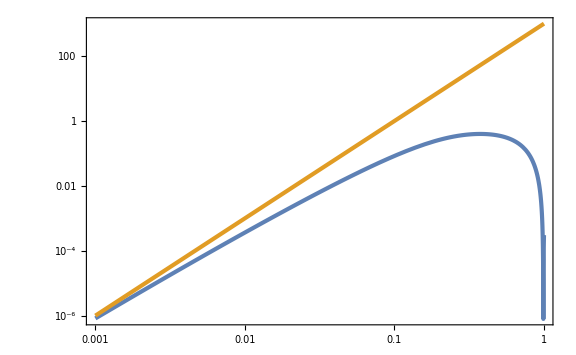

```mathematica
LogLogPlot[{3 k^2 Exp[0.01](Log[k]+0.01)^2 Erf[k Exp[0.01]/(2 0.1)],10^3 k^3},{k,10^-3,1}]
```

## Piecewise w,cs

### general

```mathematica
ρ[η_]=3/(8π)ℋ[η]^2/a[η]^2
```

(3 ℋ[η]^2)/(8 π a[η]^2)

```mathematica
ρ'[η]/.{a'[η]->ℋ[η]a[η]}//Simplify
```

-(3 (ℋ[η]^3-ℋ[η] ℋ'[η]))/(4 π a[η]^2)

```mathematica
bgEoM=Simplify[ρ'[η]==-Sqrt[24π](1+w)a[η] ρ[η]^(3/2)/.{ℋ[η]->a'[η]/a[η],ℋ'[η]->D[(a'[η]/a[η]), η]},{a'[η]>0,a[η]>0}]
```

(-1+3 w) a'[η]^2+2 a[η] a''[η]==0

```mathematica
DSolve[bgEoM,a[η],η]
```

{{a[η]→(η+3 w η-2 C[1])^(2/(1+3 w)) C[2]}}

```mathematica
aSCform[η_]=((η-ηc)/η0)^(2/(1+3w));
```

```mathematica
bgEoM/.{a[η]->aSCform[η],a'[η]->aSCform'[η],a''[η]->aSCform''[η]}//Simplify
```

True

```mathematica
ℋSCform[η_]=aSCform'[η]/aSCform[η]//Simplify
```

2/((1+3 w) (η-ηc))

```mathematica
aRDform[η_]=(η-ηc)/η0;
```

```mathematica
aRD1[η_]=aRDform[η]/.{ηc->0}
```

η/η0

```mathematica
ηSC=ηc/.Solve[aSCform[η1]==aRD1[η1],ηc][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

η1-η0 (η1/η0)^(1/2+(3 w)/2)

```mathematica
ηSC/η1/.{η1->10^-6,η0->10^5,w->0.25}
```

-22.7137

```mathematica
Normal[Series[ηSC/.{w->1/3-ϵ},{ϵ,0,2}]]
```

3/2 ϵ η1 Log[η1/η0]-9/8 ϵ^2 η1 Log[η1/η0]^2

```mathematica
aSC[η_]=aSCform[η]/.{ηc->ηSC}//Simplify
```

((η-η1+η0 (η1/η0)^(1/2+(3 w)/2))/η0)^(2/(1+3 w))

```mathematica
ηRD2=ηc/.Solve[aRDform[η2]==aSC[η2],ηc][[1]]
```

η2-η0 ((-η1+η0 (η1/η0)^(1/2+(3 w)/2)+η2)/η0)^(2/(1+3 w))

```mathematica
Normal[Series[ηRD2/.{w->1/3-ϵ},{ϵ,0,2}]]
```

-3/2 ϵ (-η1 Log[η1/η0]+η2 Log[η2/η0])-9/8 ϵ^2 (-2 η1 Log[η1/η0]+η1 Log[η1/η0]^2+2 η2 Log[η2/η0]-2 η1 Log[η1/η0] Log[η2/η0]+η2 Log[η2/η0]^2)

```mathematica
Log[10^-7/10^5]//N
```

-27.631

```mathematica
aRD2[η_]=aRDform[η]/.{ηc->ηRD2}//Simplify
```

(η-η2+η0 ((-η1+η0 (η1/η0)^(1/2+(3 w)/2)+η2)/η0)^(2/(1+3 w)))/η0

```mathematica
aRD2'[η]/aRD2[η]//Simplify
```

1/(η-η2+η0 ((-η1+η0 (η1/η0)^(1/2+(3 w)/2)+η2)/η0)^(2/(1+3 w)))

```mathematica
aSC'[η]/aSC[η]//Simplify
```

2/((1+3 w) (η-η1+η0 (η1/η0)^(1/2+(3 w)/2)))

```mathematica
ΦSCform[x_]=Φ[x]/.DSolve[Φ''[x]+(6(1+cs^2))/(1+3w)1/(x-xc)Φ'[x]+(cs^2+(12(cs^2-w))/(1+3w)^2 1/(x-xc)^2)Φ[x]==0,Φ[x],x][[1]]
```

(x-xc)^((-5-6 cs^2+3 w)/(2 (1+3 w))) BesselJ[(√(25+12 cs^2+36 cs^4+18 w-36 cs^2 w+9 w^2))/(2 (1+3 w)),cs x-cs xc] C[1]+(x-xc)^((-5-6 cs^2+3 w)/(2 (1+3 w))) BesselY[(√(25+12 cs^2+36 cs^4+18 w-36 cs^2 w+9 w^2))/(2 (1+3 w)),cs x-cs xc] C[2]

```mathematica
ΦRDform[x_]=ΦSCform[x]/.{w->1/3,cs->1/Sqrt[3]}//Simplify;
```

```mathematica
νs=(√(25+12 cs^2+36 cs^4+18 w-36 cs^2 w+9 w^2))/(2 (1+3 w));
```

```mathematica
Sqrt[νs^2+(12(cs^2-w))/(1+3w)^2]//Simplify
```

1/2 √(((5+6 cs^2-3 w)^2)/(1+3 w)^2)

```mathematica
g''[x]+(1-(2(1-3w))/(1+3w)^2 1/(x-xc)^2)g[x]/.{g[x]->Sqrt[x-xc]BesselJ[-(3(1-w))/(2(1+3w)),x-xc],g''[x]->D[D[(Sqrt[x-xc]BesselJ[-(3(1-w))/(2(1+3w)),x-xc]), x], x]}//FunctionExpand
```

0

```mathematica
g''[x]+(1-(2(1-3w))/(1+3w)^2 1/(x-xc)^2)g[x]/.{g[x]->Sqrt[x-xc]BesselY[-(3(1-w))/(2(1+3w)),x-xc],g''[x]->D[D[(Sqrt[x-xc]BesselY[-(3(1-w))/(2(1+3w)),x-xc]), x], x]}//FunctionExpand
```

0

```mathematica
ΦRD[x_]=9/x^2(Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
```

```mathematica
sSCsol=Solve[{ΦRD[k η1]==ΦSCform[k η1],ΦRD'[k η1]==ΦSCform'[k η1]}/.{xc->k ηSC},{C[1],C[2]}][[1]]//Simplify;
```

```mathematica
ΦSC[η_,k_]=Φform[k η]/.{xc->k ηSC}/.sSCsol//Simplify
```

(3 (k η0 (η1/η0)^(1/2+(3 w)/2))^((3-3 ξ)/(2+6 ξ)) (k (η-η1+η0 (η1/η0)^(1/2+(3 w)/2)))^((-5-6 cs^2+3 w)/(2+6 w)) (-BesselY[(√(25+36 cs^4+cs^2 (12-36 w)+18 w+9 w^2))/(2+6 w),cs k (η-η1+η0 (η1/η0)^(1/2+(3 w)/2))] (3 k η0 η1 (η1/η0)^(1/2+(3 w)/2) √ξ (1+3 ξ) (BesselJ[(-2-6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]-BesselJ[(2+6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]) (k η1 Cos[(k η1)/(√3)]-√3 Sin[(k η1)/(√3)])+BesselJ[(√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ] (-3 k η1 (-6 η0 (η1/η0)^(1/2+(3 w)/2) (1+3 ξ)+η1 (5+3 ξ)) Cos[(k η1)/(√3)]+√3 (-18 η0 (η1/η0)^(1/2+(3 w)/2) (1+3 ξ)+2 k^2 η0 η1^2 (η1/η0)^(1/2+(3 w)/2) (1+3 ξ)+3 η1 (5+3 ξ)) Sin[(k η1)/(√3)]))+BesselJ[(√(25+36 cs^4+cs^2 (12-36 w)+18 w+9 w^2))/(2+6 w),cs k (η-η1+η0 (η1/η0)^(1/2+(3 w)/2))] (3 k η0 η1 (η1/η0)^(1/2+(3 w)/2) √ξ (1+3 ξ) (BesselY[(-2-6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]-BesselY[(2+6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]) (k η1 Cos[(k η1)/(√3)]-√3 Sin[(k η1)/(√3)])+BesselY[(√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ] (-3 k η1 (-6 η0 (η1/η0)^(1/2+(3 w)/2) (1+3 ξ)+η1 (5+3 ξ)) Cos[(k η1)/(√3)]+√3 (-18 η0 (η1/η0)^(1/2+(3 w)/2) (1+3 ξ)+2 k^2 η0 η1^2 (η1/η0)^(1/2+(3 w)/2) (1+3 ξ)+3 η1 (5+3 ξ)) Sin[(k η1)/(√3)]))))/(k^3 η1^4 √ξ (1+3 ξ) (BesselJ[(-2-6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ] BesselY[(√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]-BesselJ[(2+6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ] BesselY[(√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]+BesselJ[(√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ] (-BesselY[(-2-6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ]+BesselY[(2+6 ξ+√((5+3 ξ)^2))/(2+6 ξ),k η0 (η1/η0)^(1/2+(3 w)/2) √ξ])))

```mathematica
ΦpSC[η_,k_]=D[ΦSC[η,k], η]//Simplify;
```

```mathematica
sRD2sol=Solve[{ΦSC[η2,k]==ΦRDform[k η2],ΦpSC[η2,k]==k ΦRDform'[k η2]}/.{xc->k ηRD2},{C[1],C[2]}][[1]]//Simplify;
```

$Aborted

```mathematica
ΦRD2[η_,k_]=ΦRDform[k η]/.{xc->k ηRD2}/.sRD2sol//Simplify;
```

### w = cs2 = 1/4

```mathematica
$Assumptions={ξ>0,η>0,η1>0,η2>0};
```

```mathematica
aSCform[η_]=((η-ηc)/η0)^(2/(1+3w))/.{w->1/4};
```

```mathematica
aRDform[η_]=(η-ηc)/η0;
```

```mathematica
aRD1[η_]=aRDform[η]/.{ηc->0}
```

η/η0

```mathematica
ηSC=ηc/.Solve[aSCform[η1]^((1+3w)/2)==aRD1[η1]^((1+3w)/2),ηc][[3]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-η0^(1/8) η1^(7/8)+η1

```mathematica
aSC[η_]=aSCform[η]/.{ηc->ηSC}//Simplify
```

((η+η0^(1/8) η1^(7/8)-η1)/η0)^(8/7)

```mathematica
ηRD2=ηc/.Solve[aRDform[η2]==aSC[η2],ηc][[1]]//Simplify
```

η2+(-η0^(1/8)+η1^(1/8)) η1^(7/8) ((η0^(1/8) η1^(7/8)-η1+η2)/η0)^(1/7)-η2 ((η0^(1/8) η1^(7/8)-η1+η2)/η0)^(1/7)

```mathematica
aRD2[η_]=aRDform[η]/.{ηc->ηRD2}//Simplify
```

(η+(η0^(1/8)-η1^(1/8)) η1^(7/8) ((η0^(1/8) η1^(7/8)-η1+η2)/η0)^(1/7)+η2 (-1+((η0^(1/8) η1^(7/8)-η1+η2)/η0)^(1/7)))/η0

```mathematica
aRD2'[η]/aRD2[η]//Simplify
```

1/(η+(η0^(1/8)-η1^(1/8)) η1^(7/8) ((η0^(1/8) η1^(7/8)-η1+η2)/η0)^(1/7)+η2 (-1+((η0^(1/8) η1^(7/8)-η1+η2)/η0)^(1/7)))

```mathematica
aSC'[η]/aSC[η]//Simplify
```

8/(7 (η+η0^(1/8) η1^(7/8)-η1))

```mathematica
ΦSCform[x_]=Φ[x]/.DSolve[Φ''[x]+(6(1+cs^2))/(1+3w)1/(x-xc)Φ'[x]+(cs^2+(12(cs^2-w))/(1+3w)^2 1/(x-xc)^2)Φ[x]==0,Φ[x],x][[1]]/.{w->ξ,cs->Sqrt[ξ]}//Simplify
```

(x-xc)^(-(5+3 ξ)/(2+6 ξ)) (BesselJ[(5+3 ξ)/(2+6 ξ),(x-xc) √ξ] C[1]+BesselY[(5+3 ξ)/(2+6 ξ),(x-xc) √ξ] C[2])

```mathematica
ΦRDform[x_]=ΦSCform[x]/.{ξ->1/3}//Simplify;
```

```mathematica
ΦRD[x_]=9/x^2(Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
```

```mathematica
sSCsol=Solve[{ΦRD[k η1]==ΦSCform[k η1],ΦRD'[k η1]==ΦSCform'[k η1]}/.{xc->k ηSC,ξ->1/4},{C[1],C[2]}][[1]]//Simplify;
```

```mathematica
ΦSC[η_,k_]=ΦSCform[k η]/.{xc->k ηSC,ξ->1/4}/.sSCsol//Simplify;
```

```mathematica
ΦpSC[η_,k_]=k ΦSCform'[k η]/.{xc->k ηSC,ξ->1/4}/.sSCsol//Simplify;
```

```mathematica
sRD2sol=Solve[{ΦSC[η2,k]==ΦRDform[k η2],ΦpSC[η2,k]==k ΦRDform'[k η2]}/.{xc->k ηRD2},{C[1],C[2]}][[1]]//Simplify
```

$Aborted

```mathematica
ΦRD2[η_,k_]=ΦRDform[k η]/.{xc->k ηRD2}/.sRD2sol//Simplify;
```

### η0 = 1, η1 = 1e-4, η2 = 1e-3, ξ = 1/4

```mathematica
η0=1;
η1=10^-4;
η2=10^-3;
ξ=1/4;
```

```mathematica
aSCform[η_]=((η-ηc)/η0)^(2/(1+3ξ));
```

```mathematica
aRDform[η_]=(η-ηc)/η0;
```

```mathematica
aRD1[η_]=aRDform[η]/.{ηc->0}
```

η

```mathematica
ηSC=ηc/.Solve[aSCform[η1]==aRD1[η1],ηc][[1]]
```

(1-√10)/10000

```mathematica
ηSC/η1//N
```

-2.16228

```mathematica
aSC[η_]=aSCform[η]/.{ηc->ηSC}//Simplify
```

((-1+√10)/10000+η)^(8/7)

```mathematica
ηRD2=ηc/.Solve[aRDform[η2]==aSC[η2],ηc][[1]]
```

(100-10^(3/7) (9+√10)^(8/7))/100000

```mathematica
aRD2[η_]=aRDform[η]/.{ηc->ηRD2}//Simplify
```

(-100+10^(3/7) (9+√10)^(8/7))/100000+η

```mathematica
Φform[x_]=Φ[x]/.DSolve[Φ''[x]+(6(1+cs^2))/(1+3w)1/(x-xc)Φ'[x]+(cs^2+(12(cs^2-w))/(1+3w)^2 1/(x-xc)^2)Φ[x]==0,Φ[x],x][[1]]
```

(x-xc)^((-5-6 cs^2+3 w)/(2 (1+3 w))) BesselJ[(√(25+12 cs^2+36 cs^4+18 w-36 cs^2 w+9 w^2))/(2 (1+3 w)),cs x-cs xc] C[1]+(x-xc)^((-5-6 cs^2+3 w)/(2 (1+3 w))) BesselY[(√(25+12 cs^2+36 cs^4+18 w-36 cs^2 w+9 w^2))/(2 (1+3 w)),cs x-cs xc] C[2]

```mathematica
ΦRD[x_]=9/x^2(Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
```

```mathematica
sSCsol=Solve[{ΦRD[k η1]==Φform[k η1],ΦRD'[k η1]==Φform'[k η1]}/.{xc->k ηSC,w->ξ,cs->Sqrt[ξ]},{C[1],C[2]}][[1]]//FullSimplify
```

{C[1]→-1/(280 10^(1/4) k^(19/14))3 π (21 k BesselY[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+2 BesselY[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)])),C[2]→1/(280 10^(1/4) k^(19/14))(63 k π BesselJ[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+6 π BesselJ[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)]))}

```mathematica
ΦSC[x_,k_]=Φform[x]/.{xc->k ηSC,w->ξ,cs->Sqrt[ξ]}/.sSCsol//Simplify
```

(25000 10^(9/28) (BesselY[23/14,((-1+√10) k)/20000+x/2] (63 k π BesselJ[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+6 π BesselJ[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)]))-3 π BesselJ[23/14,((-1+√10) k)/20000+x/2] (21 k BesselY[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+2 BesselY[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)]))))/(7 k^(19/14) ((-1+√10) k+10000 x)^(23/14))

```mathematica
ΦpSC[x_,k_]=D[ΦSC[x,k], x]//Simplify
```

(25000 10^(9/28) (-115000 (BesselY[23/14,((-1+√10) k)/20000+x/2] (63 k π BesselJ[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+6 π BesselJ[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)]))-3 π BesselJ[23/14,((-1+√10) k)/20000+x/2] (21 k BesselY[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+2 BesselY[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)])))+7/4 ((-1+√10) k+10000 x) ((BesselY[9/14,((-1+√10) k)/20000+x/2]-BesselY[37/14,((-1+√10) k)/20000+x/2]) (63 k π BesselJ[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+6 π BesselJ[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)]))-3 π (BesselJ[9/14,((-1+√10) k)/20000+x/2]-BesselJ[37/14,((-1+√10) k)/20000+x/2]) (21 k BesselY[9/14,k/(2000 √10)] (k Cos[k/(10000 √3)]-10000 √3 Sin[k/(10000 √3)])+2 BesselY[23/14,k/(2000 √10)] (3000 (210-23 √10) k Cos[k/(10000 √3)]+√3 (30000000 (-210+23 √10)+7 k^2) Sin[k/(10000 √3)])))))/(49 k^(19/14) ((-1+√10) k+10000 x)^(37/14))

```mathematica
sRD2sol=Solve[{ΦSC[k η2,k]==Φform[k η2],ΦpSC[k η2,k]==Φform'[k η2]}/.{xc->k ηRD2,w->1/3,cs->Sqrt[1/3]},{C[1],C[2]}][[1]]//Simplify;
```

```mathematica
ΦRD2[x_,k_]=Φform[x]/.{xc->k ηRD2,w->1/3,cs->Sqrt[1/3]}/.sRD2sol;
```

```mathematica
Φsol[x_,k_]:=ΦRD[x]/;x<=k η1
Φsol[x_,k_]:=ΦSC[x,k]/;k η1<x<k η2
Φsol[x_,k_]:=ΦRD2[x,k]/;k η2<=x
```

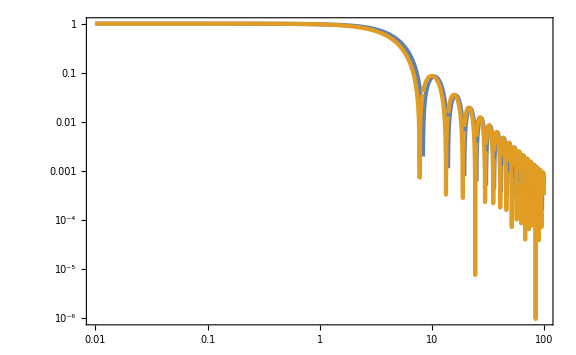

```mathematica
LogLogPlot[{Abs[Φsol[x,10^3]],Abs[ΦRD[x]]},{x,10^-2,10^2}]
```